# BTC price threshold crossings

```mathematica
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
(*Buttons to hide/show code*)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

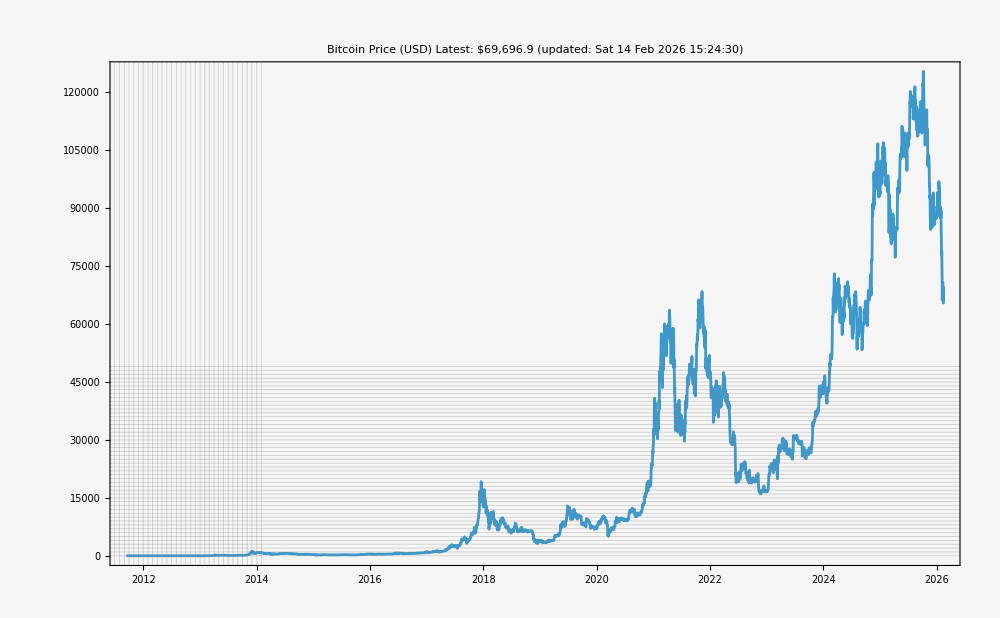
-Graphics-Threshold
USD | Times crossed
(going up)
120000 | 3
110000 | 9
100000 | 8
90000 | 11
80000 | 2
70000 | 11
60000 | 13
50000 | 12
40000 | 17
30000 | 15
20000 | 12
10000 | 14
9000 | 15
8000 | 20
7000 | 19
6000 | 6
5000 | 2
4000 | 13
3000 | 1
2000 | 3
1000 | 8
750 | 6
500 | 10
250 | 9

```mathematica
settings=<|
imagemargins->20
,imagesize->1000
,labelstyle->{14}
,origindate->"Sep. 14, 2011"
,plotbackground->Lighter[LightGray,0.75]
,subtitlestyle -> {15}
,ticksstyle->{16}
,titlestyle->{20,Red}
|>;
dollar[a_]:=StringTemplate["$``"][NumberForm[a,DigitBlock->3]];
btcDataFull = FinancialData["BTC/USD", settings[origindate]]//Normal;
plot=DateListPlot[
btcDataFull
,Background->settings[plotbackground]
,PlotLabel->Column[{
Style["Bitcoin Price (USD)",settings[titlestyle]]
,Style["Latest: "  <> dollar[btcDataFull//Last//Last],settings[subtitlestyle]]
,Style[StringForm["(updated: ``)" , DateString[]],15]
}
,Center
]
,LabelStyle->settings[labelstyle]
,GridLines->{
Join[DateRange[{2010},{2030},Quantity[1,"Months"]],{#,Thick}&/@DateRange[{2010},{2030},Quantity[1,"Years"]]]
, Join[
{#,Thickness[Tiny]}&/@Range[0,200000,1000]
,{#,Thickness[Small]}&/@Range[5000,200000,10000]
,{#,Thickness[Medium]}&/@Range[0,200000,10000]
]
}
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,FrameTicks->{All,All}
,Frame->True
];
prices = #[[2]]&/@btcDataFull;
rising=Select[
Partition[
prices,2,1]
,#[[2]]>#[[1]]&
];
tablestyle={20,GrayLevel[0.2]};
t =Table[
{Style[x,tablestyle]
,Style[
Length[
Select[
rising
,#[[2]]> x &&#[[1]]<x&
]
]
,tablestyle
]
},
{x
,Join[
Range[250,750,250]
,Range[1000,10000,1000]
,Range[20000,120000,10000]
] //Reverse
}
];
ft=Grid[
t
,Frame->All
,Spacings->{3,1}
];
ftfinal=ReplacePart[ft,1->Prepend[First[ft],{Column[Style[#,tablestyle]&/@{"Threshold","USD"},Center],Column[Style[#,tablestyle]&/@{"Times crossed","(going up)"},Center]}]];
output =Row[{
plot
,Spacer[20]
,ftfinal
}];
graphfilename = "BTC-USD-threshold-crossings.jpg";
Export[graphfilename, output];
output
```